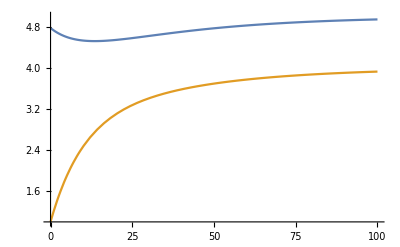

```mathematica
Plot[{-0.95056Exp[-0.028051t]+0.72499Exp[-0.10695t]+5,-1.2147Exp[-0.028051t]-1.7840Exp[-0.10695t]+4},{t,0,100}, PlotRange->{{0,100},{1,5}}]
```

```mathematica
equations = {x1''[t]==(-3x1[t]+2x2[t]), x2''[t]==(2x1[t]-3x2[t]), x1[0]==1, x1'[0]==0, x2[0]==0, x2'[0]==0}
```

{x1''[t]==-3 x1[t]+2 x2[t],x2''[t]==2 x1[t]-3 x2[t],x1[0]==1,x1'[0]==0,x2[0]==0,x2'[0]==0}

```mathematica
sol = DSolve[equations, {x1[t], x2[t]}, t]
```

{{x1[t]→1/2 (Cos[t]+Cos[√5 t]),x2[t]→1/2 (Cos[t]-Cos[√5 t])}}

```mathematica
Plot[{x1[t]/.sol, x2[t]/.sol}, {t,0,20}, PlotRange->All, PlotLabels->"Expressions"]
```

-Graphics-